```mathematica
θ0 = Pi/4
R = 100*h
μ = 3/10;
F=R*h
βц=(3*(1-μ^2))^(1/4)/Sqrt[R*h]*Sqrt[h^2]/h
βк=(3*(1-μ^2))^(1/4)/Sqrt[R/Sin[θ0]*h]*Sqrt[h^2]/h
Dц=Emod*h^3/(12*(1-μ^2))
Dк=Emod*h^3/(12*(1-μ^2))
```

π/4

100 h

100 h^2

273^(1/4)/(10 √10 h)

273^(1/4)/(10 2^(3/4) √5 h)

(25 Emod h^3)/273

(25 Emod h^3)/273

```mathematica
(*Перемещения цилиндра*)
ρцResFuncБМ[s_]=p*R^2/(Emod*h)*(1-μ/2)//Expand;
ρцResFuncКЭ1[s_]=-m/(Sqrt[2]*βц^2*Dц)*Exp[-βц*s]*Cos[βц*s+Pi/4]
ρцResFuncКЭ2[s_]=-x1/(2*βц^3*Dц)*Exp[-βц*s]*Cos[βц*s]
ρцResFuncКЭ1[0]+ρцResFuncКЭ2[0]
ρцResFunc[s_]=ρцResFuncБМ[s]+ρцResFuncКЭ1[s]+ρцResFuncКЭ2[s];
ρцResFunc[0]

υцResFunc[s_]=(D[ρцResFunc[sv],sv]/.sv->s)
```

-(20 √546 ⅇ^(-(273^(1/4) s)/(10 √10 h)) m Cos[π/4+(273^(1/4) s)/(10 √10 h)])/(Emod h)

-(200 √10 273^(1/4) ⅇ^(-(273^(1/4) s)/(10 √10 h)) x1 Cos[(273^(1/4) s)/(10 √10 h)])/Emod

-(20 √273 m)/(Emod h)-(200 √10 273^(1/4) x1)/Emod

-(20 √273 m)/(Emod h)+(8500 h p)/Emod-(200 √10 273^(1/4) x1)/Emod

(20 √273 ⅇ^(-(273^(1/4) s)/(10 √10 h)) x1 Cos[(273^(1/4) s)/(10 √10 h)])/(Emod h)+(2 273^(3/4) ⅇ^(-(273^(1/4) s)/(10 √10 h)) m Cos[π/4+(273^(1/4) s)/(10 √10 h)])/(√5 Emod h^2)+(20 √273 ⅇ^(-(273^(1/4) s)/(10 √10 h)) x1 Sin[(273^(1/4) s)/(10 √10 h)])/(Emod h)+(2 273^(3/4) ⅇ^(-(273^(1/4) s)/(10 √10 h)) m Sin[π/4+(273^(1/4) s)/(10 √10 h)])/(√5 Emod h^2)

```mathematica
(*Перемещения конуса*)
ρкResFuncБМ[s_]:=p*(R-s*Cos[θ0])^2/(Emod*h*Sin[θ0])*(1-μ/2)//Expand;
β[s_]:=Simplify[(3*(1-μ^2))^(1/4)/Sqrt[(R-s*Cos[θ0])/Sin[θ0]*h],h>0]
ρкResFuncКЭ1[s_]:=-m*Sin [θ0]/(Sqrt[2]*β[s]^2*Dк)*Exp[-β[s]*s]*Cos[β[s]*s+Pi/4]
ρкResFuncКЭ2[s_]:=-(x2+1/2*p*R*Cot[θ0])*Sin[θ0]^2/(2*β[s]^3*Dк)*Exp[-β[s]*s]*Cos[β[s]*s]
ρкResFuncКЭ1[0]+ρкResFuncКЭ2[0]
ρкResFunc[s_]:=ρкResFuncБМ[s]+ρкResFuncКЭ1[s]+ρкResFuncКЭ2[s]
ρкResFunc[0]//N//Expand

υкResFunc[s_]=Simplify[(D[ρкResFunc[sv],sv]/.sv->s)];
υкResFunc[0]//N//Expand
```

-(20 √273 m)/(Emod h)+(200 √5 546^(1/4) (50 h p-x2))/Emod

-(330.454 m)/(Emod h)+(120110. h p)/Emod-(2161.79 x2)/Emod

(2.33666 m)/(Emod h^2)+(71.4372 √(h^2) m)/(Emod h^3)-(11853.3 p)/Emod-(1146.46 √(h^2) p)/(Emod h)+(233.666 x2)/(Emod h)+(22.9292 x2)/(Emod √(h^2))

```mathematica
(*Перемещения шпангоута*)
δ22шп=R^2/(Emod*F)
ρшп=δ22шп*(x1+x2)
```

100/Emod

(100 (x1+x2))/Emod

```mathematica
(*Уравнения совместности*)
eq1=υкResFunc[0]==-υцResFunc[0];
eq2=ρкResFunc[0]==ρшп;
eq3=ρцResFunc[0]==ρшп;
Res= Simplify[(Solve[eq1&&eq2&&eq3,{m,x1,x2}]//First//Simplify),Assumptions->{h>0,s>0}];
Res//N
ρкResFunc[0]/.Res//N
ρцResFunc[0]/.Res//N
ρшп/.Res//N
Simplify[υкResFunc[0],Assumptions->{h>0}]/.Res//N
Simplify[υцResFunc[0],Assumptions->{h>0}]/.Res//N
```

{m→-12.0834 h^2 p,x1→2.62755 h p,x2→54.7534 h p}

(5738.09 h p)/Emod

(5738.09 h p)/Emod

(5738.09 h p)/Emod

(158.248 p)/Emod

-(158.248 p)/Emod

```mathematica
(*Полученные перемещения*)
```

(5738.09 h p)/Emod

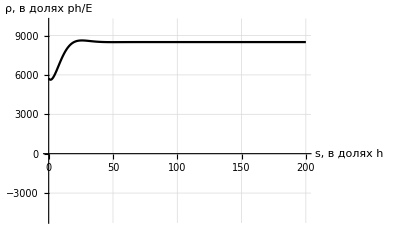

```mathematica
(*Итоговые графики перемещений*)
(*Цилиндр*)

example={h->1,Emod->1,p->1};
ρцResFunc[0]/.Res//N
Plot[ρцResFunc[s]/.Res/.example,{s,0,2*R/.example},PlotRange->{-5000, 10000},GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
```

(5738.09 h p)/Emod

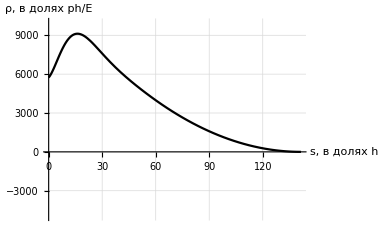

```mathematica
(*Конус*)
ρкResFunc[0]/.Res//N
Plot[ρкResFunc[s]/.Res/.example,{s,0,R/Cos[θ0]/.example},PlotRange->{-5000, 10000},GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
```

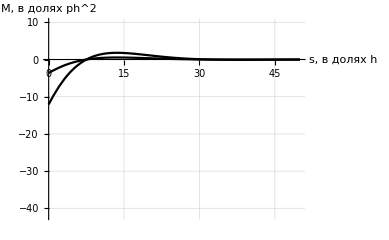

-12.0834 h^2 p

-3.62503 h^2 p

```mathematica
(*Силовые факторы*)
(*Цилиндр*)
M1цResFunc[s_]=(-Dц*D[(ρцResFuncКЭ1[sv]+ρцResFuncКЭ2[sv]),{sv,2}])/.Res/.sv->s;
M2цResFunc[s_]:=μ*M1цResFunc[s];
Plot[{M1цResFunc[s]/.example,M2цResFunc[s]/.example},{s,0,0.5*R/.example},PlotRange->{-42,10},GridLines->Automatic,AxesLabel->{"s, в долях h","M, в долях ph^2"},PlotStyle->{Black,Black}]
M1цResFunc[0]//Expand//N
M2цResFunc[0]//Expand//N
```

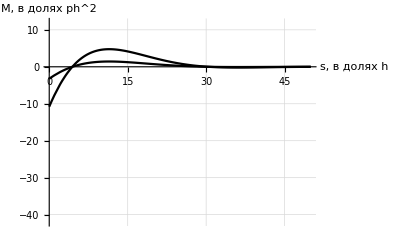

-10.7898 h^2 p

-3.23693 h^2 p

```mathematica
(*Конус*)
M1кResFunc[s_]=(-Dк/Sin[θ0]*D[(ρкResFuncКЭ1[sv]+ρкResFuncКЭ2[sv]),{sv,2}])/.Res/.sv->s;
M2кResFunc[s_]:=μ*M1кResFunc[s];
Plot[{M1кResFunc[s]/.example,M2кResFunc[s]/.example},{s,0,0.5*R/.example},PlotRange->{-42,12},GridLines->Automatic,AxesLabel->{"s, в долях h","M, в долях ph^2"},PlotStyle->{Black,Black}]
Simplify[M1кResFunc[0]//Expand,Assumptions->{h>0}]//N
Simplify[M2кResFunc[0]//Expand,Assumptions->{h>0}]//N
```

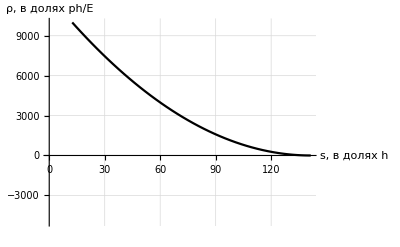

-0.155678 h^2 p

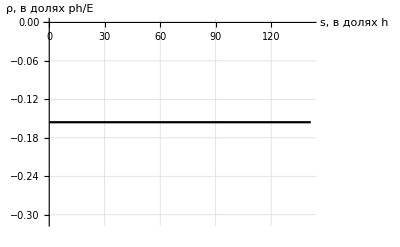

```mathematica
(*Вклад в моменты конуса от безмоментных перещемений*)
Plot[ρкResFuncБМ[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->{-5000, 10000},GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
M1кResFuncБМ[s_]=(-Dк/Sin[θ0]*D[ρкResFuncБМ[sv],{sv,2}])/.sv->s;
M1кResFuncБМ[0]//N
Plot[M1кResFuncБМ[s]/.example,{s,0,R/Cos[θ0]/.example},PlotRange->Automatic,GridLines->Automatic,AxesLabel->{"s, в долях h","ρ, в долях ph/E"},PlotStyle->{Black,Black}]
```

```mathematica
M1цTest[s_]=(-Dц*D[(ρцResFuncКЭ1[sv]+ρцResFuncКЭ2[sv]),{sv,2}])/.sv->s;
M1цTest[0]//N
M11кTest[s_]=(-Dк/Sin[θ0]*D[(ρкResFuncКЭ1[sv]),{sv,2}])/.sv->s;
M12кTest[s_]=(-Dк/Sin[θ0]*D[(ρкResFuncКЭ2[sv]),{sv,2}])/.sv->s;
Simplify[M11кTest[0],Assumptions->{h>0}]//N//Expand
Simplify[M12кTest[0],Assumptions->{h>0}]//N//Expand
```

m

1.06542 m

-21.923 h^2 p+0.438459 h x2

```mathematica
ρtest[s_]=-(x2+1/2*p*R*Cot[θ0])*Sin[θ0]^2/(2*β[s]^3*Dк)*Exp[-β[s]*s]*Cos[β[s]*s];
MTest[s_]=(-Dк/Sin[θ0]*D[(ρtest[sv]),{sv,2}])/.sv->s;
Simplify[MTest[0]//N,Assumptions->{h>0}]//Expand
```

21.923 h^2 p+0.438459 h x2

```mathematica
Simplify[D[(ρtest[sv]),{sv,1}]/.sv->0,Assumptions->{h>0}]//N//Expand
```

(12829.8 p)/Emod+(256.596 x2)/(Emod h)

```mathematica
ρкFuncКЭ1[s_]:=-m*Sin [θ0]/(Sqrt[2]*β[s]^2*Dк)*Exp[-β[s]*s]*Cos[β[s]*s+Pi/4]
M1кFuncКЭ1[s_]=(-Dк/Sin[θ0]*D[ρкResFuncКЭ1[sv],{sv,2}])/.sv->s;
Simplify[M1кFuncКЭ1[0],Assumptions->{h>0}]//N//Expand
```

1.06542 m